Server farms generate significant amounts of heat, making efficient server placement essential for lowering energy consumption. As the demand for Artificial Intelligence, cloud computing, and data processing continues to grow, so too does the need for server farms that can manage increasing thermal loads efficiently. Their growing energy consumption has challenged many, with cooling systems often accounting for up to forty percent of the total energy used in a data center. This project models heat transfer within a realistically scaled server room by numerically solving the two-dimensional heat equation using Wolfram Language. A series of visualization illustrate how different server configurations influence thermal behavior. These tools allow us to perform analysis on differing server room cooling strategies and can be extended to investigate more advanced thermal optimization techniques.

## Associated Package

Below, we will import the associated package.

```mathematica
pFileName=FileNameJoin[$HomeDirectory,"Desktop","Wolfram Notebooks","WSRP26","RecentServerPlacement.wl"];
FileExistsQ[pFileName]
```

True

```mathematica
Get[pFileName]
```

## Introduction

A server room consists of many computers operating simultaneously within an enclosed space. Each server converts part of the electrical energy it consumes into heat, creating numerous distributed heat sources throughout the room. This exchange of thermal energy can lead to localized hotspots, or, on a larger scale, heat islands. Due to the fact that this temperature distribution relies on the interaction of many heat sources over a period of time, it is difficult to predict how heat will spread through observation alone. Instead, a mathematical formula is needed to understand how heat diffuses throughout the room. This behavior is represented by the heat equation, one of the most fundamental partial differential equations in the modeling of heat transfers.

The central component of this notebook is the ServerPlacementSimulation function, which provides a framework for modeling heat transfer in server rooms. Through a collection of configurable parameters, the function enables users to simulate a wide range of server layouts, room conditions, and thermal properties. This makes it possible to reproduce all of the experiments presented in this notebook while also allowing users to investigate additional configurations and develop extensions beyond the scope of this project.

### Breaking Down The Heat Equation

There are three fundamental components needed to properly model heat flow: the partial differential equation, a defined boundary condition, and a defined initial condition. 
First, the partial differential equation. 

ρ C_p(∂T(t, X))/(∂t)+ρ C_p V·∇T(t,X)+∇·(-k ∇T(t,X))=Q

The dependent variable in this equation is the temperature, T, which varies with both time, t, and spatial position, X. The equation also accounts for the physical properties of the medium through which thermal energy is transported. These properties include the density of the medium, ρ [kg/m^3], and its specific heat capacity, C_p [J/(kg·K)].

The PDE also contains a diffusion term, ∇⋅(−k∇T(t,X)), which models the conduction of heat through the medium and is guided by the thermal conductivity, k [W/(m·K)]. In addition, a convection term, ρ C_p V·∇T(t,X) , accounts for heat transport due to airflow, where V(t,X) is the fluid velocity [m/s].

Finally, the term Q [W/m^3] represents a heat source within the region being modeled. In this project, Q corresponds to the heat produced by the servers.

While the heat equation describes how temperature diffuses over space and time, it cannot be solved without specifying both initial and boundary conditions. Initial conditions define the temperature distribution throughout the room at the start of the simulation, while boundary conditions describe how heat behaves at the boundaries in the simulation.

### Project Workflow

Before creating the simulation,  we will outline the overall approach taken throughout this project. The process of developing and evaluating the server room model was divided into four steps: defining and solving the heat equation, creating visual representations of potential layouts, performing a series of experiments on different server configurations, and evaluating the resulting temperature distributions. The following chart summarizes this workflow and provides an overview of the sections that follow.

-Graphics-

### Planned experiments

The following list outlines the experiments originally proposed for this project. Completed experiments are marked with a check mark (✓ ), while unchecked items (□) represent future investigations or possible extensions.

✓ Single-Server Configurations

Centered Placement

Random Placement

✓ Small Server Configurations

Random Placement of 2-5 servers

✓ Effect of Server Spacing

Gradually increasing the distance between servers

✓ Staggered Server Configuration

✓ Rack-Based Server Configuration

□  Cold and Hot Aisles

✓ Differently Shaped Servers

✓ Heated and Cooled Wall Boundaries

✓ Chessboard Server Configuration

✓ Hexagonal Server Configuration

✓ Room With Obstacles

Implementation-wise our main simulation function -- serverPlacementSimulation -- uses both insulating walls and cooling walls. (Via Neumann and Dirichlet boundary conditions respectively.)

## Constructing the Simulation Setup

The first and most important step in building a reliable thermal simulation is to define a reusable function that accepts the room parameters, server locations, and physical parameters as inputs before numerically solving the heat equation and returning the resulting temperature distribution.

Define the simulation function and its configurable options:

```mathematica
Clear[serverPlacementSimulation];
serverPlacementSimulation::nssh="The value of the option \"ServerShape\" is expected to be one of Automatic, Disk, or Rectangle.";
serverPlacementSimulation::nhcv="The value of the option \"HeatConvectionVelocity\" is expected to be Automatic, a number, or a list of numbers.";
```

The OverMesh option determines whether the heat equation is solved directly over the geometric region or over a finite element mesh. A mesh divides the room into many small elements, allowing the geometry of the room and server regions to be represented more accurately. The PDE is then solved numerically on these elements, which can improve the accuracy of the simulation, particularly for complex shapes or irregular boundaries.

```mathematica
Options[serverPlacementSimulation] = 
Join[
	{"ServerShape" -> Rectangle, "ServerRadius" -> 0.25, "HeatGeneration" -> 1000, "MaxTime" -> 600, 
	 "HeatConvectionVelocity" -> Automatic, "InitialRoomTemperature" -> 22, "WallSurfaceTemperature" -> 10,
	 "InsulationWalls" -> True, "OverMesh"->True},
	Options[NDSolve],
	Options[ToElementMesh]
];
```

```mathematica
optNames = {"ServerShape", "ServerRadius", "HeatGeneration", "MaxTime", "HeatConvectionVelocity","InitialRoomTemperature", "WallSurfaceTemperature", "InsulatonWalls", "OverMesh","Options[NDSolve]","Options[ToElementMesh]"};
optExplanations = {
"Specifies the shape of each server, supports either rectangular or circular (Disk) servers","Define the size for each server. In rectangular servers, this value is half the side length, while for circular servers it represents the radius",
"Specifies the rate at which each server generates heat",
"Specifies the total simulation time",
"Specifies the velocity of the fluid flow in the simulated room. When set the Autonmatic only natural diffusion is considered",
"Defines the inital uniform temperature for the room at the start of the simulation",
"Specifies the fixed temperature of the room boundaries. This allows the walls to act as heat absorbers or sources depending on their temperature relative to the room",
"Determines the thermal boundary condition at the walls. When True,insulated boundary conditions are applied so that no heat flows through the walls. When False,the walls are held at the specified surface temperature",
"Determines whether the heat equation is solved on an element mesh or a grid.Using a mesh generally improves numerical accuracy and makes it easier to handle more complex room geometries or internal obstacles",
"Includes all standard options available for NDSolve",
"Includes all options for ToElementMesh, allowing the element mesh to be refined or modified"
};
Column[{Style["Table 1. ServerPlacementSimulation Options and Descriptions",16,Bold],Grid[Prepend[Transpose[{optNames,Map[Style[#,FontFamily->"Times",FontSize->14]&,optExplanations]}],Style[#,Bold,FontFamily->"Times"]&/@{"ServerPlacementSimulation Option","Description"}],Frame->All,Alignment->{Left,Top},Background->{None,{Lighter[Gray,.95]}},Spacings->{2,1},ItemSize->{{15,50},Automatic}]},Spacings->2]
```

Table 1. ServerPlacementSimulation Options and Descriptions
ServerPlacementSimulation Option | Description
ServerShape | Specifies the shape of each server, supports either rectangular or circular (Disk) servers
ServerRadius | Define the size for each server. In rectangular servers, this value is half the side length, while for circular servers it represents the radius
HeatGeneration | Specifies the rate at which each server generates heat
MaxTime | Specifies the total simulation time
HeatConvectionVelocity | Specifies the velocity of the fluid flow in the simulated room. When set the Autonmatic only natural diffusion is considered
InitialRoomTemperature | Defines the inital uniform temperature for the room at the start of the simulation
WallSurfaceTemperature | Specifies the fixed temperature of the room boundaries. This allows the walls to act as heat absorbers or sources depending on their temperature relative to the room
InsulatonWalls | Determines the thermal boundary condition at the walls. When True,insulated boundary conditions are applied so that no heat flows through the walls. When False,the walls are held at the specified surface temperature
OverMesh | Determines whether the heat equation is solved on an element mesh or a grid.Using a mesh generally improves numerical accuracy and makes it easier to handle more complex room geometries or internal obstacles
Options[NDSolve] | Includes all standard options available for NDSolve
Options[ToElementMesh] | Includes all options for ToElementMesh, allowing the element mesh to be refined or modified

Rather than hard coding each of these values they are created as parameters within this function. This allows the same function to be reused across many simulations in which we might change the server size, heat generation, simulation time, or airflow velocity.

The simulation can be initialized in two different ways. The first accepts an integer defining the number of servers to generate randomly, while the second accepts server coordinates. This duality makes the same function suitable for random simulations and precise experiments.

The first definition of the simulation function serves to generate random server layouts. It accepts the number of servers, the room dimensions, the simulation duration, and additional options. Using these inputs, the function randomly generates valid server coordinates within the boundaries of the room. These generated coordinates, together with the original simulation parameters, are then passed to the second definition of the function, where the heat transfer simulation is constructed and solved.

```mathematica
serverPlacementSimulation[n_?IntegerQ, roomWidth_?NumericQ, roomHeight_
	?NumericQ, opts : OptionsPattern[]] :=
	Module[{spec, serverRadius, minX, maxX, minY, maxY},
		serverRadius = OptionValue[serverPlacementSimulation, "ServerRadius"];
		maxX = roomWidth;
		maxY = roomHeight;
		{minX, minY} = {0, 0};
		spec = Transpose[{
			RandomReal[{minX + serverRadius, maxX - serverRadius}, n],
			RandomReal[{minY + serverRadius, maxY - serverRadius}, n]}];
		serverPlacementSimulation[spec, roomWidth, roomHeight, opts]
	];
```

The second definition of serverPlacementSimulation is what creates the main simulation. This version accepts an  list of server coordinates. This makes it possible to test defined layouts, such as dense racks, sparse arrangements, or optimized configurations.

The function then constructs the room shape, defines the server heat-source regions, retrieves the physical properties of the medium, builds the heat transfer PDE, and solves it numerically.

```mathematica
serverPlacementSimulation[spec : {{_?NumericQ, _?NumericQ}..}, roomWidth_
	?NumericQ, roomHeight_?NumericQ, opts : OptionsPattern[]] :=
	Module[{minX = 0, minY = 0, maxX, maxY, serverShape, serverRadius, heatGeneration,
		 tend, insolationWallsQ, overMeshQ, Ω2D, Ω, mesh, serverRegions, sourceRegion, rmf, vars, pars, pde, Tfun, 
		kAir, cpAir, ρAir, velocity, initRoomTemp, wallSurfaceTemp, wall},
		serverShape = OptionValue[serverPlacementSimulation, "ServerShape"];
		serverRadius = OptionValue[serverPlacementSimulation, "ServerRadius"];
		heatGeneration = OptionValue[serverPlacementSimulation, "HeatGeneration"];
		velocity = OptionValue[serverPlacementSimulation, "HeatConvectionVelocity"];
		initRoomTemp = OptionValue[serverPlacementSimulation, "InitialRoomTemperature"];
		wallSurfaceTemp = OptionValue[serverPlacementSimulation, "WallSurfaceTemperature"];
		tend = OptionValue[serverPlacementSimulation, "MaxTime"];
		insolationWallsQ = TrueQ[OptionValue[serverPlacementSimulation, "InsulationWalls"]];
		overMeshQ = TrueQ[OptionValue[serverPlacementSimulation, "OverMesh"]];
		serverShape =
			Which[
			TrueQ[serverShape === Automatic],Rectangle,
			MemberQ[{Rectangle, Disk}, serverShape],serverShape,
			True,Message[serverPlacementSimulation::nssh];
			Return[$Failed]
			];
		velocity =
			Which[
			TrueQ[velocity === Automatic],{0, 0},
			NumericQ[velocity],{velocity, 0},
			VectorQ[velocity, NumericQ] && Length[velocity] == 1,{velocity[[1]], velocity[[1]]},
			VectorQ[velocity, NumericQ] && Length[velocity] >= 2,velocity[[1 ;; 2]],
			True, Message[serverPlacementSimulation::nhcv];
			Return[$Failed]
			];
		maxX = roomWidth;
		maxY = roomHeight;
		kAir = QuantityMagnitude[ThermodynamicData["Air", "ThermalConductivity"]];
		cpAir = QuantityMagnitude[ThermodynamicData["Air", "IsobaricHeatCapacity"]];
		ρAir = QuantityMagnitude[ThermodynamicData["Air", "Density"]];
		vars = {T[t, x, y], t, {x, y}};
		Ω2D = Rectangle[{minX, minY}, {maxX, maxY}];
		serverRegions = 
		If[TrueQ[serverShape===Rectangle],
			Rectangle[# - {serverRadius, serverRadius}, # + {serverRadius, serverRadius}]& /@ spec,
			Disk[#, serverRadius]& /@ spec];
		sourceRegion=RegionUnion @@ serverRegions;
		Ω=RegionDifference[Ω2D, sourceRegion];
		mesh=If[overMeshQ,
			ToElementMesh[Ω, Evaluate[FilterRules[{opts}, Options[ToElementMesh]]], "RegionHoles"->None],
			None];
		rmf = RegionMember[sourceRegion];
		pars =<|"ThermalConductivity" -> kAir,"MassDensity" -> ρAir,"SpecificHeatCapacity" -> cpAir,"HeatConvectionVelocity" -> velocity,"HeatSource" ->
			With[{Qg = heatGeneration, rmfLocal = rmf},
				If[rmfLocal[{x, y}], Qg, 0]]|>;
pde = If[insolationWallsQ,{HeatTransferPDEComponent[vars, pars] == NeumannValue[0, x == minX || x == maxX || y == minY || y == maxY], T[0, x, y] == initRoomTemp},
wall=HeatTemperatureCondition[x == minX || x == maxX || y == minY || y == maxY, vars, pars, <|"SurfaceTemperature"->wallSurfaceTemp|>];
{HeatTransferPDEComponent[vars,pars]==0, wall, T[0, x, y] == initRoomTemp}];
Tfun = NDSolveValue[pde, T, {t, 0, tend}, {x, y} ∈ If[overMeshQ,mesh,Ω2D], FilterRules[{opts}, Options[NDSolve]]];
<|"Spec" -> spec, "Solution" -> Tfun, "RoomHeight" -> maxY, "RoomWidth" -> maxX, "Region" -> Ω2D, "FieldRegion" -> Ω, "Mesh" -> mesh|>
]
```

The secondary definition of this function can be broken down into six main steps. First, it reads the user-specified options, including server size, heat generation, simulation time, and convection velocity. Second, it constructs the room as a rectangular domain.  Third, it represents each server as a rectangular heat-generating region. Fourth, it retrieves the thermal conductivity, density, and specific heat capacity of air from Wolfram’s thermodynamic database. Fifth, it uses these quantities to construct the heat transfer PDE with HeatTransferPDEComponent. Finally, NDSolveValue solves the PDE and returns an association containing the server specification, the solved temperature function, and the room dimensions.

## Using Proper Metrics

### Creating Realistic Rooms

Throughout each of the below experiments the room dimensions, airflow velocity, heat generation, and simulation time were selected using values representative of real server rooms. The server radius was treated as an adjustable parameter, allowing different server sizes and packing densities to be investigated throughout the experiments

The heat generation parameter represents the rate at which thermal energy is produced by each server and is measured in watts (J/s). Because the  heat equation is solved over time, the total amount of thermal energy introduced into the system depends on both the heat generation rate and the duration of the simulation.

Server layouts are initially generated on a dimensionless integer grid. These integer coordinates define only the relative positions of the servers and are independent of any units. The coordinates are then scaled according to the selected server radius and room dimensions, producing meaningful server locations while preserving the  arrangement. This approach allows the same layout to be reused across multiple experiments with different server sizes and room dimensions without modifying the underlying grid.

### Computing Statistics

Throughout each experiment, it is necessary to compute statistics of the temperature distribution in order to identify trends and compare different server configurations. Although the serverPlacementSimulation function solves the heat equation and produces the temperature distribution over time, an additional function is required to extract meaningful metrics from this solution. Specifically, this function computes the minimum, average, and maximum temperatures of the system at a specified point in time, enabling consistent quantitative comparisons between different layouts.

To begin constructing this function, Clear is first used to remove any previously assigned values. The available options are then defined, allowing the server shape and server radius to be specified later when the function is called.

```mathematica
Clear[metricGeneration];
Options[metricGeneration] = Join[{"ServerShape"->Rectangle, "ServerRadius" ->0.25}];
```

The metricGeneration function accepts the interpolating temperature solution, simulation time, and room dimensions as inputs. It first retrieves the specified server radius and server shape from the function options, then determines the appropriate area. The function subsequently computes the maximum, minimum, and average temperatures using Maximum, Minimum, and NIntegrate, respectively.

```mathematica
metricGeneration[Tfun_,plotTime_,roomWidth_,roomHeight_,opts : OptionsPattern[]]:=
Module[{avgTemp,area,gridMax,gridMin,gridAvg, serverRadius, serverShape,temps},
serverRadius = OptionValue[metricGeneration, "ServerRadius"];
serverShape = OptionValue[metricGeneration, "ServerShape"];
Which[
MemberQ[{Rectangle,"Rectangle"},serverShape],area=roomWidth*roomHeight;
MemberQ[{Disk,"Disk"},serverShape],area=(serverRadius^2)*Pi;
True, Return[$Failed]
];
avgTemp =NIntegrate[Tfun[plotTime,x,y],{x,0,roomWidth},{y,0,roomHeight},MinRecursion->4,PrecisionGoal->4]/area;
temps=Flatten[Table[Tfun[plotTime,x,y],{x,0,roomWidth,roomWidth/20},{y,0,roomHeight,roomHeight/20}]];
gridMin=Min[temps];
gridMax=Max[temps];
gridAvg=Mean[temps];
<|"Average" -> avgTemp, "GridAverage" -> gridAvg, "GridMinimumTemperature" -> gridMin, "GridMaximumTemperature" ->gridMax|>
]
```

## Constructing a Realistically Scaled Server Room

There is no single way to arrange servers within a room. Different layouts produce different airflow paths, heat concentrations, and cooling requirements. To investigate how configuration influences thermal behavior, several different placement strategies were constructed and simulated.

### Single Server - Baseline

The simplest possible server room consists of a single server positioned within the room. This baseline establishes a reference against which more complex layouts can later be compared. Since only one heat source is present, the resulting temperature distribution is expected to be relatively symmetric, making it easier to verify that the model behaves as expected before introducing additional servers.

The room is first defined as an 9×9 computational grid. At this stage, the coordinates simply represent potential server locations rather than realistic distances. A random point on the graph is selected to behave as the server and the selected server position is demarcated with a red dot.

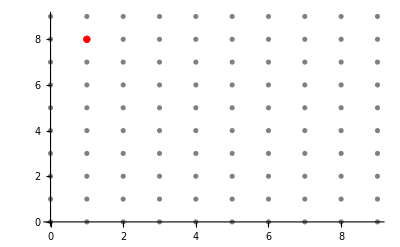

```mathematica
serverPositions = Partition[Flatten[Table[{i,j}, {i,0,9}, {j, 0,9}]],2];
chosenPoints = RandomSample[serverPositions,1];
Show[
ListPlot[serverPositions,PlotStyle->Gray],
ListPlot[chosenPoints,PlotStyle->Red]
]
```

A minimum spacing rule will now be used so that adjacent servers are separated by at least one server width. Because each server is modeled as 0.50 m wide, adjacent server centers must be at least 0.5 m apart. This prevents unrealistic overlap and creates a more physically reasonable server-room layout.

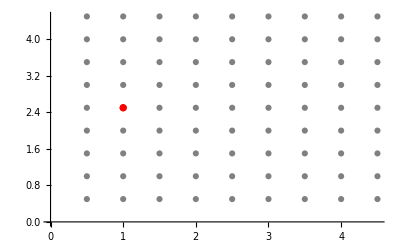

```mathematica
SeedRandom[34];
serverPositions = Partition[Flatten[Table[{i,j}, {i,1,9}, {j,1,9}]],2];
chosenPoints = RandomSample[serverPositions,1];

scale = 0.5;
scaledServerPostions = scale*serverPositions;
scaledChosenPoints = scale*chosenPoints;
Show[
ListPlot[scaledServerPostions,PlotStyle->Gray],
ListPlot[scaledChosenPoints,PlotStyle->Red]
]
```

With the properly scaled server location now established, the serverPlacementSimulation function can be used to solve the heat equation. Using the server as the sole heat source and using defined physical parameters, the function solves for the resulting temperature distribution throughout the room.

```mathematica
nRows = 9;
nColumns=9;
roomWidth=scale*nColumns;
roomHeight=scale*nRows;
result=serverPlacementSimulation[scaledChosenPoints,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->1000/3600,"MaxTime"->6000, "InsulationWalls"->True,"InitialRoomTemperature"->10,"WallSurfaceTemperature"->10,MaxCellMeasure->0.05]
```

<|Spec→{{1.,2.5}},Solution→InterpolatingFunction[…],RoomHeight→4.5,RoomWidth→4.5,Region→Rectangle[{0,0},{4.5,4.5}],FieldRegion→Polygon[…],Mesh→ElementMesh[{{0.,4.5},{0.,4.5}},{TriangleElement[<648>]}]|>

The resulting solution can now be visualized using a temperature map. This provides a view of how thermal energy spreads throughout the room from the server heat source.

```mathematica
Tfun = result["Solution"];
ContourPlot[Tfun[6000,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotRange->All,PlotPoints->150]//Rasterize
```

-Graphics-

While the temperature map provides a qualitative visualization of the solution, it is also useful to quantify the behavior of the room. To accomplish this, the minimum, maximum, and average temperatures throughout the room are computed after the simulation reaches its final time.

For every set of server coordinates, the serverPlacementSimulation function solves the heat equation, after which the resulting interpolating temperature function is passed to metricGeneration to compute the minimum, maximum, and average temperatures using both continuous and grid-based methods. The computed metrics are then stored in an association and compiled into a tabular dataset for comparison.

```mathematica
plotTime = 600;
serverRadius = 0.25;
listOfPositions={scaledChosenPoints};
opts={"ServerRadius"->0.25,"HeatGeneration"->1000/3600,"MaxTime"->6000,"InsulationWalls"->True,"InitialRoomTemperature"->10,"WallSurfaceTemperature"->10,MaxCellMeasure->0.05};
results=Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,opts];
resultingSoln=aRes["Solution"];
n=Length[coord];
metrics = metricGeneration[resultingSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = metrics["GridMinimumTemperature"];
gridMaxTemp = metrics["GridMaximumTemperature"];
gridAvgTemp = metrics["GridAverage"];
avgTemp = metrics["Average"];
<|"Coordinates"->coord,"Servers"->n,"AvgTemp"->avgTemp, "GridAverageTemperature" ->gridAvgTemp,"GridMinimumTemperature"->gridMinTemp,"GridMaximumTemperature"-> gridMaxTemp|>,{coord,listOfPositions}];
tblData = Tabular[results]
```

Since only one heat source is present, the temperature distribution remains relatively uniform throughout the room. The average room temperature remains close to the initial temperature of 10, while the maximum temperature reaches approximately 10.12 at the server location. The minimum temperature remains at the initial room temperature, indicating that the heat generated by a single server has only a localized effect. These values serve as a baseline against which configurations containing multiple servers can be compared.

### Creating an Interactive Server Room Simulation

To allow for further analysis, we developed an interactive interface. This interface allows the user to adjust simulation parameters, including the room dimensions, number of servers, server size, heat generation, and simulation time. By immediately visualizing the effects of these changes on the temperature distribution, the interface provides a platform for exploring how different design choices influence the thermal behavior of a server room before conducting more experiments.

The Manipulate controls change the number of servers, room size, simulation time, and server radius. Each time these parameters are updated, serverPlacementSimulation recomputes the heat equation solution, and the resulting temperature field is displayed as a contour plot.

```mathematica
DynamicModule[{aRes,Tfun,spec,minX,maxX,minY,maxY,width, height,insulationWalls, nServersOld=-1,roomHeightOld = -1,roomWidthOld = -1,opts},
opts={"HeatGeneration"->1000/3600,"InsulationWalls"->insulationWalls,"InitialRoomTemperature"->10,"WallSurfaceTemperature"->10,MaxCellMeasure->0.05};
Manipulate[
If[nServers!=nServersOld ||roomHeight!=roomHeightOld ||roomWidth!=roomWidthOld||insulationWalls!=insulationWallsOld,
nServersOld=nServers;
roomHeightOld=roomHeight;
roomWidthOld = roomWidth;
insulationWallsOld=insulationWalls;
aRes=serverPlacementSimulation[nServers,roomWidth,roomHeight,"ServerRadius"->serverRadius,"MaxTime"->plotTime,opts],
aRes=serverPlacementSimulation[spec,roomWidth,roomHeight,"ServerRadius"->serverRadius,"MaxTime"->plotTime,opts]
];
Tfun=aRes["Solution"];
spec=aRes["Spec"];
height = aRes["RoomHeight"];
width = aRes["RoomWidth"];
{minX,minY}={0,0};
{maxX,maxY}={roomWidth,roomHeight};
Show[
ContourPlot[Tfun[plotTime,x,y],{x,minX,maxX},{y,minY,maxY},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,AspectRatio->Automatic,ImageSize->{Automatic,350}],
Graphics[{Black,Rectangle[#-{serverRadius,serverRadius},#+{serverRadius,serverRadius}]&/@spec}]],
{{nServers,3,"Number of Servers"},1,10,1},
{{roomWidth,4,"Room Width"},4,16,1},{{roomHeight,4,"Room Height"},4,16,1},
{{plotTime,600,"Time"},0,6000,50},
{{serverRadius,0.25,"server radius"},0.20,1,0.05},
SaveDefinitions->True
]
]
```

```mathematica
DynamicModule[{aRes,Tfun,spec,minX,maxX,minY,maxY,width,height,nServersOld=-1,roomHeightOld=-1,roomWidthOld=-1,insulationWallsOld=True,opts},
Manipulate[
opts={"HeatGeneration"->1000/3600,"InsulationWalls"->insulationWalls,"InitialRoomTemperature"->10,"WallSurfaceTemperature"->10,MaxCellMeasure->0.05};
If[
nServers!=nServersOld||roomHeight!=roomHeightOld||roomWidth!=roomWidthOld||insulationWalls!=insulationWallsOld,nServersOld=nServers;
roomHeightOld=roomHeight;
roomWidthOld=roomWidth;
insulationWallsOld=insulationWalls;
aRes=serverPlacementSimulation[nServers,roomWidth,roomHeight,"ServerRadius"->serverRadius,"MaxTime"->plotTime,Sequence@@opts],aRes=serverPlacementSimulation[spec,roomWidth,roomHeight,"ServerRadius"->serverRadius,"MaxTime"->plotTime,Sequence@@opts]
];
Tfun=aRes["Solution"];
spec=aRes["Spec"];
height=aRes["RoomHeight"];
width=aRes["RoomWidth"];
{minX,minY}={0,0};
{maxX,maxY}={roomWidth,roomHeight};
Show[
ContourPlot[Tfun[plotTime,x,y],{x,minX,maxX},{y,minY,maxY},ColorFunction->"TemperatureMap",PlotLegends->Automatic,PlotRange->All,AspectRatio->Automatic,ImageSize->{Automatic,350}],
Graphics[{Black,Rectangle[#-{serverRadius,serverRadius},#+{serverRadius,serverRadius}]&/@spec}]],
{{nServers,3,"Number of Servers"},1,10,1},
{{roomWidth,4,"Room Width"},4,16,1},
{{roomHeight,4,"Room Height"},4,16,1},
{{plotTime,600,"Time"},0,6000,50},
{{serverRadius,0.25,"Server Radius"},0.20,1,0.05},
{{insulationWalls,True,"Insulation Walls"},{True,False}},
SaveDefinitions->True
]
]
```

The If determines whether a new server layout needs to be generated. If the number of servers or room dimensions changes, then serverPlacementSimulation is called using the number of servers, which randomly generates a new configuration. If only the simulation time or server radius changes, the existing server coordinates are reused so that the same layout can be evaluated without randomizing the server positions again.

This simulation allowed for a few key observations. The relative placement of the servers had a significant influence on hotspot formation. Servers positioned close to one another consistently reached higher temperatures than isolated servers, leading to localized heat accumulation. A similar effect was observed near the room boundaries, where servers placed adjacent to walls tended to reach higher temperatures than those located nearer the center of the room.

### Determining Optimal Spacing Between Square Servers

The previous experiments suggested that the spacing between servers has a significant impact on heat distribution. To investigate this relationship more systematically, the distance between neighboring servers was varied while other simulation parameters were held constant.

Next, the parameters for solving the heat equation at each of these positions must be defined. A 5 .0 m × 5.0  m room with small servers is sufficient for this experiment because the objective is to study the relationship between the distance between two servers and the resulting heat distribution.

```mathematica
roomWidth =5;
roomHeight = 5;
plotTime = 10*3600;
serverRadius = 0.25;
```

The first step is to generate a sequence of server positions that will be evaluated. Each pair of coordinates places the servers progressively closer together, ensuring that server spacing is the only variable changing between simulations.

```mathematica
nExperiments=30;
listOfNumbers=Table[{{h,roomHeight/2},{roomWidth-h,roomHeight/2}},{h,2*serverRadius, roomWidth/2-1.5serverRadius,serverRadius/2}];
```

Now, these parameters and coordinates will be plugged into the serverPlacementSimulation function and metricGeneration function to retrieve the minimum, maximum, and average temperature reached for each configuration.

```mathematica
opts={"HeatGeneration"->3000,"InsulationWalls"->True,"InitialRoomTemperature"->22,"WallSurfaceTemperature"->10,MaxCellMeasure->0.05};
results=Quiet@Table[
aRes =serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->serverRadius,"MaxTime"->plotTime,opts];
resultingSoln=aRes["Solution"];
metrics = metricGeneration[resultingSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->serverRadius,MaxIterations->1000, PrecisionGoal->6];
n =Length[coord];
gridMinTemp = metrics["GridMinimumTemperature"];
gridMaxTemp = metrics["GridMaximumTemperature"];
gridAvgTemp = metrics["GridAverage"];
avgTemp = metrics["Average"];
If[Length[coord]>=2,gap=EuclideanDistance@@coord[[1;;2]];
amountOfServersBetween=gap/(serverRadius*2),
(*ELSE*)
gap=Missing["NotEnoughServers"];
amountOfServersBetween=Missing["NotEnoughServers"];
];

<|"Coordinates"->coord,"Servers"->n,"AvgTemp" ->avgTemp,"Gap"->gap,"RescaledGap" ->amountOfServersBetween, "GridAvgTemp" ->gridAvgTemp, "GridMaxTemp"->gridMaxTemp, "GridMinTemp"->gridMinTemp|>,{coord,listOfNumbers}
];

tblData = Tabular[results]
```

Remark: We use the function Quiet in order to suppress warning messages. (Not error messages.)

The data collected in the table above can be visualized using a scatter plot to examine the relationship between server spacing and the maximum room temperature, making it easier to identify trends.

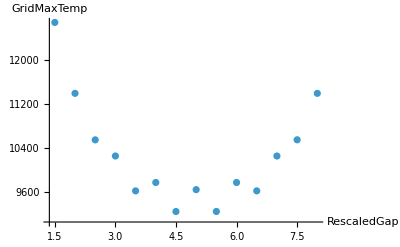

```mathematica
Values/@Normal[tblData[[All, {"Gap","GridMaxTemp"}]]];
columnNames= {"RescaledGap","GridMaxTemp"};
ListPlot[Values/@Normal[tblData[[All,columnNames]]],PlotRange->All,AxesLabel->columnNames]
```

Thanks to this visualization, it can be observed that as servers are closer to one another or the walls of the room the heat they generate increases profoundly. Furthermore, the distance between two servers that resulted in the lowest maximum temperature is 4.50 servers apart. This makes sense with the inital prediction as the servers are relatively far apart; however, are not overly near the walls.

### Chessboard Configuration

While increasing the distance between servers generally improves heat concentration, it also reduces the number of servers that can fit within a room. In practice, an optimal layout must balance heat with space. To investigate this, a checkerboard configuration was simulated. By placing servers on alternating grid positions,  gaps are introduced between neighboring servers while still maintaining a relatively high density.

The first step in creating this grid was to define a 8 x 10 grid.

Grid points were then selected to create a checkerboard pattern, so that each server was separated from one another by an empty grid position. Finally, the selected coordinates were scaled to realistic dimensions.

```mathematica
nRows=8;
nColumns=10;
scale=0.5;
serverRadius=0.25;
gridPoints=Flatten[Table[{j,i},{i,1,nRows-1},{j,1,nColumns-1}],1];
checkerboardPoints=Select[gridPoints,EvenQ[Total[#]]&];
gridPointsScaled=scale*gridPoints;
checkerboardPointsScaled=scale*checkerboardPoints;
```

Following this, the parameters for the Server Placement Simulation function, such as roomWidth, roomHeight, and plotTime, are defined. The coordinates for the selected servers alongside these parameters are then fed into the function and the solution is stored.

```mathematica
roomWidth=scale*nColumns;
roomHeight=scale*nRows;
plotTime=600;
result=serverPlacementSimulation[checkerboardPointsScaled,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->plotTime,"OverMesh"->False];
Tfun=result["Solution"];
```

The solution stored above is then qualitatively visualized below as a temperature map.

```mathematica
ContourPlot[Tfun[600,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->50]//Rasterize
```

-Graphics-

To properly compare the chessboard configuration with the other layouts, performance metrics, specifically the minimum, maximum, and average temperatures, must first be computed using the metricGeneration and serverPlacementSimulation functions.

```mathematica
result=serverPlacementSimulation[checkerboardPointsScaled,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->plotTime,"OverMesh"->False];
resultingSoln=result["Solution"];
metrics = metricGeneration[resultingSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
a=<|"Servers"->Length[checkerboardPointsScaled],"AvgTemp" ->avgTemp,"GridAvgTemp" ->gridAvgTemp, "GridMaxTemp"->gridMaxTemp, "GridMinTemp"->gridMinTemp|>;
tblData = Tabular[{a}]
```

Upon comparing this table with the two-server configuration, it can be seen that the maximum temperature is higher than the largest maximum temperature observed in the two-server case. This suggests that the chessboard configuration does not distribute heat as effectively, despite introducing gaps between neighboring servers.

### Disk Configuration

In an effort to further optimize the functionality of server farms, we hypothesize that circular servers could utilize natural convection patterns to substitute for cooling equipment. Below, we will experiment with the shape of the servers to determine whether a circular server allows for better convection than a square server.  We are creating a simulation that is very similar to the single square server experiment, solely changing the shape to be able to obtain an accurate comparison.

As completed previously, a grid of potential positions is generated and scaled to realistic sizing. The position of the server is selected randomly and stored.

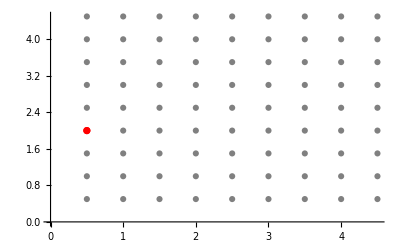

```mathematica
circleServerPositions = Partition[Flatten[Table[{i,j}, {i,1,9}, {j,1,9}]],2];
circleChosenPoints = RandomSample[serverPositions,1];

scale = 0.5;
circleScaledServerPostions = scale*circleServerPositions;
circleScaledChosenPoints = scale*circleChosenPoints;
Show[
ListPlot[circleScaledServerPostions,PlotStyle->Gray],
ListPlot[circleScaledChosenPoints,PlotStyle->Red]
]
```

Once the location of our server has been generated we will call the serverPlacementSimulation function to solve the heat equation. However, unlike previously, we will specify the option “ServerShape” as a Disk.

Using these defined parameters, the function solves for the resulting temperature distribution throughout the room.

```mathematica
nRows = 9;
nColumns=9;
roomWidth=scale*nColumns;
roomHeight=scale*nRows;
circleResult=serverPlacementSimulation[circleScaledChosenPoints,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->1000,"MaxTime"->6000,"ServerShape" -> Disk];
```

Once more, we will be visualizing the resulting solution using a temperature map. We can compare how thermal energy spreads throughout the room from the circular server heat source versus the previous visualization of circular server heat sources.

```mathematica
Tfun = circleResult["Solution"];
ContourPlot[Tfun[1000,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->50,PlotRange->All]//Rasterize
```

-Graphics-

We will once again compute the minimum, maximum, and average temperatures throughout the room after the simulation reaches its final time.

```mathematica
listOfPositions={circleScaledChosenPoints};
circleResults=Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->600];
resultingSoln=aRes["Solution"];
n=Length[coord];
metrics = metricGeneration[resultingSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = metrics["GridMinimumTemperature"];
gridMaxTemp = metrics["GridMaximumTemperature"];
gridAvgTemp = metrics["GridAverage"];
avgTemp = metrics["Average"];
<|"Coordinates"->coord,"Servers"->n,"AvgTemp"->avgTemp,"GridAvgTemp" ->gridAvgTemp, "GridMaxTemp"->gridMaxTemp, "GridMinTemp"->gridMinTemp|>,{coord,listOfPositions}];
tblData = Tabular[circleResults]
```

Compared with the square-server results in both the chessboard and two-server configurations, the circular servers consistently produce a significantly lower maximum grid temperature. This suggests that the circular geometry may improve heat distribution. However, this comparison may be influenced by the fact that a circle has a smaller surface area than the corresponding square, resulting in a smaller heat-generating region. To isolate the effect of geometry from surface area, the following experiment controls for the area of each server, allowing the impact of shape alone to be evaluated.

### Disk versus Square

To enable a more accurate comparison between disk-shaped and square-shaped servers, both configurations will be evaluated using identical coordinate positions on the grid. This ensures that server placement remains constant, allowing any differences in heat distribution to be attributed solely to the server shape. For each configuration, the maximum and average temperatures will be calculated and compared to determine whether disk-shaped or square-shaped servers produce higher temperatures, or whether it is effectively the same.

First, we must generate the grid of possible server positions and choose a random position for both to input into the Server Placement Simulation function.

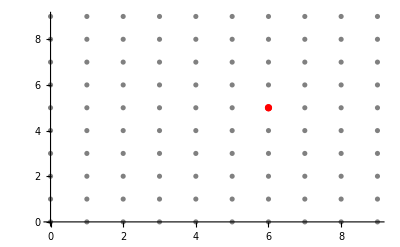

```mathematica
bothServerPositions=Partition[Flatten[Table[{i,j},{i,0,9},{j,0,9}]],2];bothChosenPoints=RandomSample[serverPositions,1];
Show[
ListPlot[bothServerPositions,PlotStyle->Gray],
ListPlot[bothChosenPoints,PlotStyle->Red]
]
```

We then solve the heat equation for both configurations using the serverPlacementSimulation function, and the resulting temperature values are recorded in separate tables for comparison.

To ensure a fair comparison between square and disk-shaped servers, both shapes must occupy the same area. Since the square server has a side length of 0.25, its area is 0.0625. The radius of the disk is then chosen so that its area, πr^2, is also equal to 0.0625. Solving this equation gives a disk radius of approximately 0.141. Using equal areas ensures that any differences in heat distribution are due to the server geometry rather than the size of the heat source.

```mathematica
nRows=9;nColumns=9;roomWidth=scale*nColumns;roomHeight=scale*nRows;listOfPositions={scaledChosenPoints};bothCircleresults=Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->0.141,"HeatGeneration"->1000,"MaxTime"->600,"ServerShape"->Disk];resultingCircleSoln=aRes["Solution"];n=Length[coord];circleMetrics = metricGeneration[resultingCircleSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = circleMetrics["GridMinimumTemperature"];
gridMaxTemp = circleMetrics["GridMaximumTemperature"];
gridAvgTemp = circleMetrics["GridAverage"];
minTemp= circleMetrics["MinimumTemperature"];
maxTemp= circleMetrics["MaximumTemperature"];
avgTemp = circleMetrics["Average"];
<|"Coordinates"->coord,"Servers"->n,"AvgTemp"->avgTemp,"GridAvgTemp" ->gridAvgTemp, "GridMaxTemp"->gridMaxTemp, "GridMinTemp"->gridMinTemp|>,{coord,listOfPositions}];
Echo["Circle Results"]
tblData=Tabular[bothCircleresults] 

bothSquareresults=Quiet@Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->1000,"MaxTime"->600,"ServerShape"->Rectangle];resultingSquareSoln=aRes["Solution"];n=Length[coord];squareMetrics = metricGeneration[resultingSquareSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = squareMetrics["GridMinimumTemperature"];
gridMaxTemp = squareMetrics["GridMaximumTemperature"];
gridAvgTemp = squareMetrics["GridAverage"];
minTemp= squareMetrics["MinimumTemperature"];
maxTemp= squareMetrics["MaximumTemperature"];
avgTemp = squareMetrics["Average"];
<|"Coordinates"->coord,"Servers"->n,"AvgTemp"->avgTemp,"GridAvgTemp" ->gridAvgTemp, "GridMaxTemp"->gridMaxTemp, "GridMinTemp"->gridMinTemp|>,{coord,listOfPositions}];
Echo["Square Results"]
tblData=Tabular[bothSquareresults]
```

Circle Results

Circle Results

Square Results

Square Results

Remark: We use the function Quiet in order to suppress warning messages. (Not error messages.)

Interestingly, the circular server configuration generally produced lower maximum and average temperatures than the square configuration. However, the square servers typically resulted in slightly lower minimum temperatures. This could suggest that, although circular servers tend to reduce overall heat accumulation, square servers may allow for slightly cooler regions to develop elsewhere in the room.

### Constructing a Server Room with Racks

In many server farms, servers are not simply placed individually throughout a room. To maximize space efficiency, servers are typically organized into groups known as server racks. These racks allow a large number of servers to be housed in a compact area, making efficient use of floor space while facilitating power distribution, and cooling. To account for this, we will conduct an experiment that evaluates the heat distribution of a system in which servers are grouped together into racks.

This grid is created using the serverPosition function, which creates a grid of points arranged into server racks. The function is parameterized by number of columns and number of rows, allowing different rack configurations to be generated easily.

```mathematica
Clear[serverPositions];
serverPositions[nRows_,nColumns_]:=Flatten[Table[{j,i},{i,2,nRows-1,1},{j,2,nColumns-2,2}],1];
```

The room is first defined as an 8 × 10 computational grid. At this stage, the coordinates simply represent potential server locations rather than realistic distances.

```mathematica
{nRows,nColumns}={8,10};
```

Two sets of coordinates are then generated. The first contains every possible location within the room, while the second contains only those positions that will be occupied by servers.

```mathematica
gridPoints=Flatten[Table[{j,i},{i,nRows},{j,nColumns}],1];
serverPoints=serverPositions[nRows,nColumns];
```

This grid is then converted into realistic physical dimensions. Within our simulation each server occupies a 0.50 m × 0.50 m area; therefore, every coordinate is multiplied by a scaling factor of 0.50. This transforms the grid into a realistically sized 5 m × 4 m server room.

```mathematica
scale=0.5;
gridPointsScaled=scale*gridPoints;
serverPointsScaled=scale*serverPoints;
```

Finally, both sets of coordinates are plotted. The blue points represent every possible server location within the room, while the orange points indicate the locations occupied by servers.

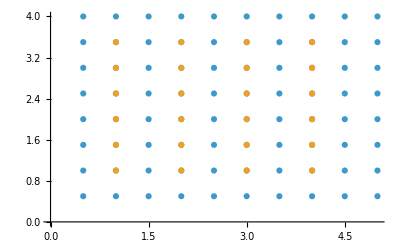

```mathematica
ListPlot[{gridPointsScaled,serverPointsScaled}]
```

The room dimensions are then scaled, and these parameters, together with the selected server locations, are passed as inputs to the serverPlacementSimulation function, which solves the Heat Equation.

```mathematica
roomWidth=scale*nColumns;
roomHeight=scale*nRows;
serverPointsScaled = scale*serverPoints;
result=serverPlacementSimulation[serverPointsScaled,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->1000,"MaxTime"->600,"OverMesh"->False];
```

The output of the serverPlacementSimulation function is returned as an association containing all information required for subsequent analysis. The interpolating function represents the numerical solution to the Heat Equation and can be evaluated at any point within the room, providing the basis for both visualization and the computation of thermal metrics .

```mathematica
Tfun=result["Solution"];
ContourPlot[Tfun[600,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->50]//Rasterize
```

-Graphics-

I will now calculate the average, maximum, and minimum temperature for each of the servers in this server farm configuration which includes four racks.

```mathematica
listOfPositions
```

{{{0.5,2.}}}

```mathematica
plotTime=600;
serverRadius=0.25;
scale=0.5;

nRows=9;
nColumns=9;
roomWidth=scale*nColumns;
roomHeight=scale*nRows;

serverPoints=serverPositions[nRows,nColumns];
serverPointsScaled=scale*serverPoints;
listOfPositions=List/@serverPointsScaled;
results=Quiet@Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->600, "OverMesh"->False];
resultingSoln=aRes["Solution"];
n=Length[coord];
metrics = metricGeneration[resultingSoln,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = metrics["GridMinimumTemperature"];
gridMaxTemp = metrics["GridMaximumTemperature"];
gridAvgTemp = metrics["GridAverage"];
avgTemp = metrics["Average"];
<|"Coordinates"->coord,"Servers"->n,"AvgTemp"->avgTemp,"GridMaxTemp"->gridMaxTemp, "GridAvgTemp"->gridAvgTemp, "GridMaxTemp"->gridMaxTemp|>,{coord,listOfPositions}];
tblData = Tabular[results]
TabularSummary[tblData]
```

Remark: We use the function Quiet in order to suppress warning messages. (Not error messages.)

### Hexagonal Grids

In previous experiments, servers were placed on a rectangle, where each server location is equally spaced in the horizontal and vertical directions. While this provides a simple way to evaluate heat distribution, it does not necessarily represent the most efficient arrangement. To investigate an potential layout, this experiment uses a hexagonal grid, in which each server location has six nearby positions. This is one of the most efficient ways to arrange objects, allowing a greater density of servers while maintaining uniform spacing. Because server density and spacing directly influence heat transfer, evaluating a hexagonal grid provides insight into how alternative packing affects  the temperature distribution throughout the room.

To begin, we initialize the serverGridPoints function and define its configurable options. These options control how the hexagonal grid is generated, allowing the spacing and positioning of the grid to be adjusted while ensuring that valid input values are provided.

```mathematica
Clear[serverGridPoints];
serverGridPoints::nsf="The value of the option \"ServerFactor\" is expected to be numeric.";
serverGridPoints::noff="The value of the option \"Offset\" is expected to be Automatic or numeric.";

Options[serverGridPoints]={Exclusions->None,"Offset"->Automatic,"StepFactor"->1/100};
```

The serverGridPoints function takes in the room dimensions, a tile shape, and a tile size, then generates a hexagonal grid across the room. The function creates a list of evenly spaced coordinate points within the room and passes them into ResourceFunction[“HextileBins”], which groups those points into hexagonal tile regions. Finally, the function returns the hexagonal polygons that make up the grid.

```mathematica
serverGridPoints[
	{roomWidth_?IntegerQ,roomHeight_?IntegerQ},tileShape:("Hextile"|"Tile"),tileSize_?NumericQ,opts:OptionsPattern[]]:=
		Module[{sf,offset,coords,polys},
		sf=OptionValue[serverGridPoints,"StepFactor"];
		If[!NumberQ[sf],Message[serverGridPoints::nsf]; Return[$Failed]];
		offset=OptionValue[serverGridPoints,"Offset"];
		If[TrueQ[offset===Automatic],offset=tileSize];
		If[!NumberQ[offset],
		Message[serverGridPoints::noff]; Return[$Failed]
		];
coords=Flatten[Table[{i,j},{i,offset,roomWidth-offset,roomWidth*sf},{j,offset,roomHeight-offset,roomHeight*sf}],1];
polys=Keys@ResourceFunction["HextileBins"][coords,tileSize];
polys
];
```

The function serverGridPoints constructs a hexagonal grid for a room measuring 16 × 12 units with a tile size of 1 unit. The generated hexagonal polygons are stored in the variable polys.

```mathematica
polys=serverGridPoints[{16,12},"Hextile",2];
```

Finally, the generated hexagonal grid is visualized.

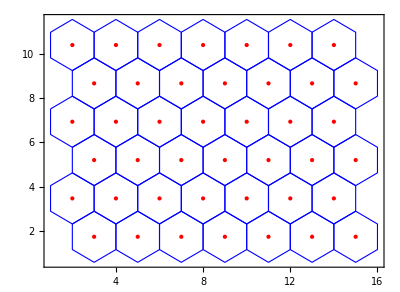

```mathematica
Graphics[{FaceForm[None],EdgeForm[Blue],polys,Red,Point[Mean@*PolygonCoordinates/@polys]},Frame->True]
```

Now that the hexagonal grid has been generated, it can be used to evaluate the thermal behavior of the system. Each grid point represents a possible server location, allowing the heat equation to be solved across different placements and the resulting temperature distribution to be compared.

Below, the center of each hexagon is used to create a list of server locations.

```mathematica
centerCoords = Mean@*PolygonCoordinates/@polys;
```

These coordinates are then passed to the serverPlacementSimulation function to compute the resulting heat distribution for each placement.

Remark: We use the function Quiet in order to suppress warning message. (Not error messages.)

Now that the grid has been visualized we proceed by simulating and plotting the solution:

```mathematica
result=serverPlacementSimulation[centerCoords,16,12,"ServerRadius"->0.25,"HeatGeneration"->4000/3600,
"MassDensity" -> 1, "SpecificHeatCapacity" -> 1,"MaxTime"->30000,"InsulationWalls" -> False,"InitialRoomTemperature" -> 18, "WallSurfaceTemperature" ->5, MaxCellMeasure-> 0.05];
```

```mathematica
Tfun = result["Solution"];
plotTime=20000;
Show[
ContourPlot[Tfun[20000,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->350,PlotRange->All,AspectRatio->Automatic,ImageSize->600,FrameTicks->Automatic,PlotLabel->Row[{"Hexagonal cell size:",cellSize," m , at time:",plotTime," s"}]],
RegionPlot[RegionDifference[result["Region"],result["FieldRegion"]],PlotStyle->{GrayLevel[0.2]}]
]
```

-Graphics-

Now that the solution has been plotted we will quantitatively evaluate the metrics for this configuration using the metricGeneration function.

```mathematica
metrics = metricGeneration[Tfun,plotTime,roomWidth,roomHeight,"ServerShape"->Rectangle, "ServerRadius" ->0.25];
gridMinTemp = metrics["GridMinimumTemperature"];
gridMaxTemp = metrics["GridMaximumTemperature"];
gridAvgTemp = metrics["GridAverage"];
avgTemp = metrics["Average"];
assoc = Association["MaxTemp"->gridMaxTemp,"MinTemp"->gridMinTemp,"AvgTemp"->avgTemp, "gridAvgTemp"->gridAvgTemp];
Dataset[assoc]
```

### Hexagonal Grids with Obstacles

Oftentimes, server rooms don’t consist of unobstructed rectangular spaces. Structural features such as columns, pipes, cooling infrastructure, and electrical equipment can reduce the area available for server placement. To account for these real-world obstacles, we simulate a large obstacle at the center of the room, representing a physical obstruction such as a pipe or support column. A hexagonal grid is then generated around this obstacle, allowing us to investigate how restricted server placement influences heat distribution and to identify optimal server locations under these conditions.

A large set of random candidate points is first generated throughout the room. Any points that fall inside a circular region at the center of the room, representing the obstacle, are then removed. The remaining points define the valid locations from which the hexagonal grid will be constructed.

```mathematica
n=5000;{roomWidth,roomHeight}={10,8};rRoom=Rectangle[{0,0},{roomWidth,roomHeight}];coords=Transpose[{RandomReal[{0,roomWidth},n],RandomReal[{0,roomHeight},n]}];coords2=Select[coords,!RegionMember[Disk[{roomWidth,roomHeight}/2,2.5],#]&];
```

The coordinate points are then passed to the HextileBins resource function, which groups the points into a hexagonal tiling with a tile size of 0.5 units. The resulting collection of hexagonal polygons is stored in the variable polys.

```mathematica
polys=Keys@ResourceFunction["HextileBins"][coords2,0.5];
polys//Length;
```

Finally, the generated hexagonal grid is visualized. The center points represent the candidate server locations that will be used in the subsequent heat distribution simulations.

```mathematica
Graphics[{FaceForm[None],EdgeForm[Blue],polys,Red,Point[Mean@*PolygonCoordinates/@polys]}]
```

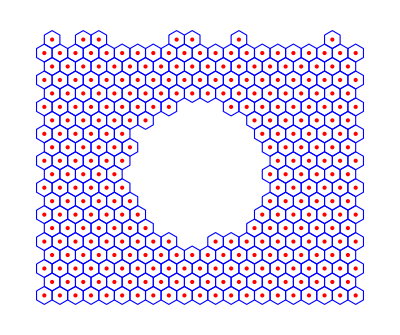

-Graphics-

Now that our hexagonal grid has been generated with an obstacle in the center, we can evaluate the thermal behavior of a more realistic room. Once again, each grid point represents is the center of a server , allowing the heat equation to be solved across different placements and the resulting temperature distribution to be compared.

To begin, we extract the center points for each of the hexagons which be used to represent each individual server.

```mathematica
centerCoords = Mean@*PolygonCoordinates/@polys;
positions=centerCoords[[1;;10]];
listOfPositionsHexHole = List/@positions;
```

These coordinates are then passed to the serverPlacementSimulation function to compute the resulting heat distribution for each placement.

```mathematica
plotTime=600;
serverRadius=0.25;
results=Table[aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->plotTime,"OverMesh"->False];
Tfun=aRes["Solution"];
n=Length[coord];
temps=Flatten[Table[Tfun[plotTime,x,y],{x,0,roomWidth,roomWidth/20},{y,0,roomHeight,roomHeight/20}]];
minTemp=Min[temps];
maxTemp=Max[temps];
avgTemp=Mean[temps];
<|"Coordinates"->coord,"Servers"->n,"MinTemp"->minTemp,"MaxTemp"->maxTemp,"AvgTemp"->avgTemp|>,{coord,listOfPositionsHexHole}];
tblData = Tabular[results]
TabularSummary[tblData]
```

We will now again use a density plot to visualize how thermal energy spreads throughout this grid for a specific server.

```mathematica
coord=listOfPositionsHexHole[[1]];
aRes=serverPlacementSimulation[coord,roomWidth,roomHeight,"ServerRadius"->serverRadius,"HeatGeneration"->1000,"MaxTime"->plotTime];
Tfun=aRes["Solution"];
ContourPlot[Tfun[plotTime,x,y],{x,0,roomWidth},{y,0,roomHeight},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->150,PlotRange->All]
```

-Graphics-

### Comparing Differently Sized Hexagonal Grids

One objective is to determine the appropriate level of spatial density needed for the analysis. A finer hexagonal grid may reveal localized findings that would otherwise be hidden, whereas a coarser grid may be better for estimating the overall thermal behavior.

To investigate the effect of spatial resolution, the room was partitioned using different hexagon sizes . A bin size of 1 produces a finer grid with more hexagons, while a bin size of 2 results in a coarser grid consisting of fewer, larger cells . Comparing these two allows us to evaluate how sensitive the measured thermal patterns are to the chosen spatial resolution and determine whether a coarse approximation is sufficient or if finer detail is necessary to identify localized hotspots .

To begin, we must first define the parameters that will be used to visualize both experiments -- the room size, boundaries, and coordinate points for server locations.

```mathematica
n=5000;{roomWidth,roomHeight}={10,10};rRoom=Rectangle[{0,0},{roomWidth,roomHeight}];coords=Transpose[{RandomReal[{2,roomWidth-2},n],RandomReal[{2,roomHeight-2},n]}];coords2=Select[coords,!RegionMember[Disk[{roomWidth,roomHeight}/2,2.5],#]&];
```

The coordinate points are then passed to the HextileBins resource function, which groups the points into a hexagonal tiling. The resulting collection of hexagonal polygons is stored in the variable polys.

```mathematica
cellSize=1;
polys=Keys@ResourceFunction["HextileBins"][coords2,cellSize];
polys//Length;
```

The center coordinates of these polygons are then pulled and stored to visualize the hexagonal grid.

```mathematica
centerCoords= Mean@*PolygonCoordinates/@polys;
```

Finally, the generated hexagonal grid is visualized. The center points represent the candidate server locations that will be used in the subsequent heat distribution simulations. The below grid is for a cellSize of one. Similar calculations were performed for a grid with a cell size of two.

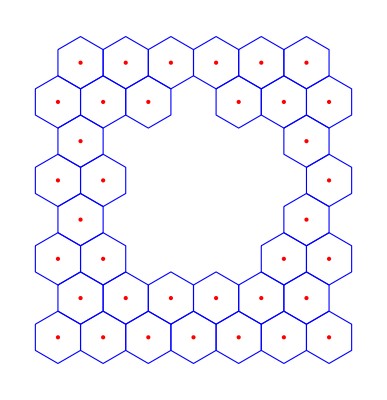

```mathematica
Graphics[{FaceForm[None],EdgeForm[Blue],polys,Red,Point[Mean@*PolygonCoordinates/@polys]}]
```

This evaluation has two main parts: first we run the heat simulation.

```mathematica
result=serverPlacementSimulation[centerCoords,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->4000/3600,
"MassDensity" -> 1, "SpecificHeatCapacity" -> 1,"MaxTime"->30000,"InsulationWalls" -> False,"InitialRoomTemperature" -> 18, "WallSurfaceTemperature" ->5, MaxCellMeasure-> 0.05];
```

Second, we plot the temperature field for the two different hexagonal cell sizes.

```mathematica
Tfun = result["Solution"];
plotTime=20000;
gr[cellSize]=Show[
ContourPlot[Tfun[20000,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->350,PlotRange->All,AspectRatio->Automatic,ImageSize->400,FrameTicks->Automatic,PlotLabel->Row[{"Hexagonal cell size:",cellSize," m , at time:",plotTime," s"}]],
RegionPlot[RegionDifference[result["Region"],result["FieldRegion"]],PlotStyle->{GrayLevel[0.2]}]
];
```

```mathematica
Row[{gr[1],gr[2]}]
```

Comparing the two visualizations shows that a hexagonal grid with a cell size of 1 captures a much greater concentration of localized heat than a grid with a cell size of 2. The finer discretization preserves more detailed thermal information and highlights hotspots that become less pronounced when larger hexagonal cells are used.

## Making the Headline Image

The headline image for this notebook was generated using cooled room boundaries rather than other cooling methodologies. In this model, the cooled walls serve as a simplified representation of active cooling systems, such as fans or air-conditioning units, which remove heat from the server room. While this approximation captures the overall effect of cooling, incorporating airflow and fan models remains a future extension we hope to complete.

Finally, the finite element mesh generated by the simulation was refined using MaxCellMeasure -> 0.05, producing a smoother numerical solution and higher-quality visualization. The resulting temperature field was then plotted to create the headline image shown at the beginning of this notebook.

The first step was to define a 9 x 16 room representing the dimensions of the server room . A list of server coordinates was then created manually using Table, placing servers in three evenly spaced horizontal rows to produce a clean and visually balanced arrangement . These coordinates were stored in scaledChosenPoints3 and supplied directly to the simulation function, ensuring that the server placement remained fixed rather than randomly generated .

The surrounding walls were held at a fixed temperature of 5 degrees Celsius by setting “InsulationWalls” -> False and specifying “WallSurfaceTemperature” -> 5, allowing the boundaries to remove heat from the room . This simplified boundary condition acts as an approximation of an active cooling system, producing a temperature distribution while maintaining an efficient model . The simulation was run for 30,000 time units, allowing the solution to approach a stable temperature distribution .

```mathematica
nRows = 9;
nColumns=16;
roomWidth=nColumns;
roomHeight=nRows;
scaledChosenPoints3=Flatten[Table[{i,roomHeight*f},{i,3,roomWidth-2,2},{f,{1,2,3}/4}],1];
result=serverPlacementSimulation[scaledChosenPoints3,roomWidth,roomHeight,"ServerRadius"->0.25,"HeatGeneration"->4000/3600,
"MassDensity" -> 1, "SpecificHeatCapacity" -> 1,"MaxTime"->30000,"InsulationWalls" -> False,"InitialRoomTemperature" -> 18, "WallSurfaceTemperature" ->5, MaxCellMeasure-> 0.05];
```

Before solving the heat equation, this configuration is visualized to ensure that it has been constructed correctly. The first command, displays the overall region while the second displays the squares that represent servers.

```mathematica
RegionPlot[result["FieldRegion"],AspectRatio->Automatic]//Rasterize
RegionPlot[RegionDifference[result["Region"],result["FieldRegion"]],AspectRatio->Automatic]//Rasterize
```

-Graphics-

-Graphics-

Finally, we created a visualization of how the temperature spreads within this configuration using the solution from serverPlacementSimulation and a ContourPlot.

```mathematica
Tfun = result["Solution"];
Show[
ContourPlot[Tfun[60,x,y],{x,0,result["RoomWidth"]},{y,0,result["RoomHeight"]},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotPoints->350,PlotRange->All,AspectRatio->Automatic,ImageSize->1000,FrameTicks->None,PlotLegends->None],
RegionPlot[RegionDifference[result["Region"],result["FieldRegion"]],PlotStyle->{GrayLevel[0.2]}],
Graphics[{EdgeForm[GrayLevel[0.7]],Opacity[0.4],FaceForm[None],Rest@result["Mesh"]["Wireframe"][[1]]}]
]//Rasterize
```

-Graphics-

## Observations

We developed a simulation framework that enables reproducible investigations of heat transfer within server rooms. By exposing  physical parameters, the framework allows a wide variety of thermal scenarios to be simulated while maintaining a consistent methodology for comparison. Throughout the experiments presented in this notebook, several expected trends emerged.

In particular, servers placed in close proximity to one another produced higher localized temperatures due to the overlap of their thermal fields. Likewise, servers positioned near insulated boundaries retained more heat, resulting in increased maximum and average room temperatures.

The framework also enabled comparisons between alternative server shapes. Across nearly all of the configurations examined, circular servers produced lower maximum and average temperatures than rectangular servers under comparable conditions.

Beyond reproducing expected physical behavior, the framework provides a platform for exploring what-if scenarios relevant to server room design. The experiments presented here examined the effects of server geometry, server placement, spacing between servers, and different thermal boundary conditions, including insulated and actively cooled walls. Because the simulation framework is highly configurable, it can readily be extended to investigate additional layouts, cooling strategies, airflow models, and optimization techniques, making it a useful tool for future studies of data center thermal management.

## Future Directions

Several extensions could be explored to improve or expand the heat simulation model.

### Cellular Automata

One possible direction is to use a cellular automata model instead of directly solving the heat equation. In this approach, the room would be divided into a grid of small cells, where each cell stores a temperature value. At each time step, the temperature of a cell would be updated based on the temperatures of its neighboring cells. Servers could be represented as cells that continuously add heat, while walls or cooling regions could remove heat. This method would be easier to implement and visualize, while still capturing the general idea of heat spreading through a room.

### Custom Heat Simulation Rule

Another possible extension is to define a custom heat simulation rule rather than relying on a partial differential equation. For example, the temperature at each point could be updated using a manually designed rule that accounts for heat generation, diffusion to nearby regions, cooling from walls, and airflow. This would allow more control over the assumptions of the model and make it easier to experiment with simplified or approximate heat-transfer behavior.

### Manual Equation Construction

Another extension would be to continue using the PDE-based heat model, but construct the equation manually rather than relying on built-in Wolfram components. Instead of using a predefined heat-transfer setup, the model could explicitly define the two-dimensional heat equation, including terms for diffusion, internal heat generation from servers, and optional convection from airflow. This would make the mathematics behind the equation more visible and allow more precise modifications to the equation.

### Dirichlet Conditions for the server walls

In this experiment, we have created an option to modify the boundary conditions for the walls using Neumann and Dirichlet conditions. This means that the walls can either insulate heat or  cool. However, the model could also be extended by experimenting with Dirichlet boundary conditions for the servers themselves. This means that the servers could either insulate heat or cool, allowing for an interesting analysis of different configurations.

In this project, an option was implemented to modify the wall boundary conditions using either Neumann or Dirichlet boundary conditions. With Neumann conditions, the walls are insulated, preventing heat from flowing across the boundaries, whereas Dirichlet conditions hold the walls at a fixed temperature, allowing them to act as cooling surfaces. An extension of this model would be to apply Dirichlet boundary conditions to the servers themselves. Rather than modeling servers only as heat sources, their surfaces could be maintained at  temperatures, representing  cooled servers. Investigating combinations of cooled and insulated servers would enable a more realistic analysis of modern data center cooling strategies.

### Hot and Cold Aisles

In addition, servers could be arranged into alternating hot and cold aisles, similar to real data center layouts . Cold aisles would represent regions where cool air is supplied, while hot aisles would collect warmer exhaust air . Comparing these layouts could help determine how server arrangement and boundary cooling influence the formation of hotspots and overall room temperature.

## References

[WR1] Wolfram Research (2020-2026), "Room Heating", Wolfram tech note, https://reference.wolfram.com/language/PDEModels/tutorial/SystemPhysics/ModelCollection/RoomHeating.html
[WR2] Wolfram Research (2024), “Modeling Heat Transfer in Server Rooms,” Wolfram Broadcast Video, https://www.wolfram.com/broadcast/video.php?c=370&disp=list&v=675&p=1
[WRIf1] Wolfram Research (2020), HeatTransferPDEComponent,  Wolfram Language Function, https://reference.wolfram.com/language/ref/HeatTransferPDEComponent.html (updated 2026)

## Acknowledgements

I would like to thank my mentor, Dr. Anton Antonov, for his guidance and expertise throughout this project. His knowledge and support were vital in both the development of the simulation framework and the completion of this research. I am especially grateful for his patience and willingness to help me overcome the many challenges encountered along the way.

I would also like to thank the Wolfram Research Summer Program directors -- Megan, Rory, and Eryn -- for their  support, organization, and encouragement throughout the program. Additionally I would like to thank my TA, Divya Thota, my mentor group, and my TA group.

Finally, I would like to thank Stephen Wolfram and Wolfram Research for providing me with the opportunity to participate in the Wolfram Summer Research Program. I am truly grateful for the opportunity to learn from such an exceptional community.